## Alzheimer’s Disease Research ADAPT In SC - Winthrop University

## Numerical Simulation of Aβ and Ca Compartments

### Parameter Choices (Arbitrary at the Moment)

```mathematica
a1 = 0.01;
a2=0.05;
b1=1000;
b2=20;
k1=0.00002617;
k2=0.1;
α1=0.5;
α2=0.5;
δ1=0.4;
δ2=0.4;
σ=0.00027;
r1 = k1 + (1-α1)*δ1;
r2=k2 + (1-α2) * δ2;
```

### Computation

```mathematica
soln=NDSolve[{ABeta'[t]==a1 - r1 * ABeta[t] + a2 * Ca[t]/(Ca[t]+σ),Ca'[t]==b1 - r2 * Ca[t] + b2*ABeta[t],ABeta[0]==0.0,Ca[0]==0.0},{ABeta,Ca},{t,0,40}];
numericalequil = NSolve[{a1 - r1 * ABeta + a2 * Ca/(Ca+σ)==0,b1 - r2 * Ca + b2*ABeta==0,ABeta>=0,Ca>=0},{ABeta,Ca}]
```

{{ABeta→0.299961,Ca→3353.33}}

```mathematica
(*values=Table[{t,ABeta[t]/. soln//First,Ca[t]/. soln//First},{t,0,40,0.1}];*)
```

```mathematica
(*values*)
```

### Visualization

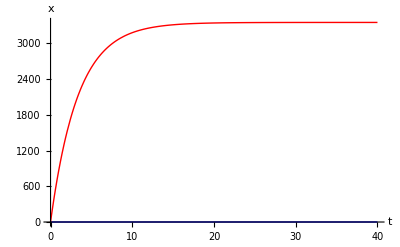

```mathematica
Plot[Evaluate[{ABeta[t],Ca[t]}/.soln],{t,0,40},PlotStyle->{{Blue,Thick},{Red,Thick}},AxesLabel->{t,x},PlotRange->All]
```

## Full Compartmental Model Simulation

Using the parameter values for the two compartment model above, the relevant parameter are appended here and observed.

```mathematica
a1 = 0.01;
a2=0.05;
b1=1000;
b2=20;
k1=0.00002617;
k2=0.1;
σ=0.00027;
c1=0.000000097;
k3=0.000708;
c2 = 0.001;
c3= 0.001;
d1=0.01;
e1=1.67;
e2=3.83;
KN=1.00;
KC=169.48;
α1=0.1;
α2=0.1;
α3=0.1;
δ1=0.04;
δ2=0.04;
δ3=0.04;
r1 = k1 + (1-α1)*δ1;
r2=k2 + (1-α2) * δ2;
r3 = k3+(1-α3)*δ3;
```

```mathematica
DAβ = a1-r1*Aβ+a2*Ca/(Ca+σ);
DCa = b1-r2*Ca+b2*Aβ;
Dτ=c1-r3*τ+c2*Aβ+c3*Ca;
DN = d1*τ(1-N/KN);
DC=(e1*N+e2*τ)*(1-C/KC);

equilsol = NSolve[{DAβ==0,DCa==0,Dτ==0,DN==0,DC==0,Aβ>=0,Ca>=0,τ>=0,N>=0,C>=0},{Aβ,Ca,τ,N,C}]
```

{{Aβ→1.66546,Ca→7597.86,τ→207.026,N→1.,C→169.48}}